### Introduction

Consider the representation x = (1 | 0 | 1 | 1
0 | 1 | 1 | rⅇ^ⅈθ) and y = (y_11 | y_12
y_21 | y_22
y_31 | y_32
y_41 | t) where the  are uniquely determined by .  For each  triple I’ve generated a new representation in the same orbit solving  where .  When , the values of  parametrize polygon space.  Given a fixed , increasing  corresponds to flowing up along the moment map induced by the -action.  The short subsets are , and these subsets are straight when  is 0, 1, and ∞ respectively.  These are the most interesting points to flow up from.  I reparametrized  so that the short subsets are straight when  is .

### The Program

```mathematica
(*Imports data.  Takes ~3 mins to load.  Change to "hyperpolygonDataLowRes" for ~25 sec version*)
SetDirectory[NotebookDirectory[]];
hyperpolygonData=ToExpression[Import["hyperpolygonDataPolar"],TraditionalForm];
{rRange,θRange,tRange,hyperpolygonVals}=hyperpolygonData;

(*Basis of su(2)*)
b1=({{0, ⅈ}, {ⅈ, 0}});b2=({{0, 1}, {-1, 0}});b3=({{ⅈ, 0}, {0, -ⅈ}});

(*Writes elements of -ⅈsu(2) as vectors in Reals^3*)
ToCoordinates[A_]=1/2{Tr[ⅈ b1.A],Tr[ⅈ b2.A],Tr[ⅈ b3.A]};

(*Given a representation x∈Hom(C^4,C^2), y∈Hom(C^2,C^4), this displays the hyperpolygon in Reals^3*)
ShowHyperpolygon=Function[{x,y},
Module[{v,w,vertices,hyperpolygon,plotBounds},
v=Table[x[[All,i;;i]].x[[All,i;;i]]†,{i,1,4}];
w=Table[y[[i;;i,All]]†.y[[i;;i,All]],{i,1,4}];

(*Creates vertices of polygon*)
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+ToCoordinates[v[[i]]]];
AppendTo[vertices,Last[vertices]-ToCoordinates[w[[i]]]],
{i,1,4}];

(*Draws lines between vertices*)
hyperpolygon={};
Do[AppendTo[hyperpolygon,Black];
AppendTo[hyperpolygon,Line[{vertices[[i]],vertices[[i+1]]}]];
AppendTo[hyperpolygon,Darker@Green];
AppendTo[hyperpolygon,Line[{vertices[[i+1]],vertices[[i+2]]}]],
{i,1,7,2}];

(*Creates graph*)
plotBounds={Min[#,-.2],Max[#,.2]}&/@(Re[vertices]ᵀ);
Graphics3D[{Thickness[.006],hyperpolygon},Background->White,Axes->True,AxesLabel->{b1,b2,b3},PlotRange->plotBounds,ImageSize->Large,AspectRatio->1]
]
];

c1=({{0, 1}, {0, 0}});c2=({{1, 0}, {0, -1}});c3=({{0, 0}, {1, 0}});
SL2Coordinates[A_]=1/2{Tr[c1.A],Tr[c2.A],Tr[c3.A]};

ShowSL2Polygon=Function[{x,y},
Module[{u,vertices,SL2RealPolygon,SL2ImaginaryPolygon,plotBoundsReal,plotBoundsImaginary},
u=Table[x[[All,i;;i]].y[[i;;i,All]],{i,1,4}];

(*Creates vertices of polygon*)
vertices={{0,0,0}};
Do[AppendTo[vertices,Last[vertices]+SL2Coordinates[u[[i]]]],
{i,1,4}];

(*Draws lines between vertices*)
SL2RealPolygon=Line[Re@vertices];
SL2ImaginaryPolygon=Line[Im@vertices];

(*Creates graph*)
plotBoundsReal={Min[#,-.02],Max[#,.02]}&/@(Re[vertices]ᵀ);
plotBoundsImaginary={Min[#,-.02],Max[#,.02]}&/@(Im[vertices]ᵀ);
{Graphics3D[{Thickness[.006],SL2RealPolygon},Background->White,Axes->True,AxesLabel->{c1,c2,c3},PlotRange->plotBoundsReal,ImageSize->Medium,AspectRatio->1],
Graphics3D[{Thickness[.006],SL2ImaginaryPolygon},Background->White,Axes->True,AxesLabel->{c1,c2,c3},PlotRange->plotBoundsImaginary,ImageSize->Medium,AspectRatio->1]}
]
];

(*Sets bounds for Manipulate[]*)
{rMin,rMax,Δr}=rRange;
{θMin,θMax,Δθ}=θRange;
{tMin,tMax,Δt}=tRange;

(*3D array of values for x and y*)
xVals=hyperpolygonVals[[All,All,All,1]];
yVals=hyperpolygonVals[[All,All,All,2]];


(*Interpolates data*)
xFunctionValuedMatrix=Table[ListInterpolation[xVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,2},{j,1,4}];
yFunctionValuedMatrix=Table[ListInterpolation[yVals[[All,All,All,i,j]],{{rMin,rMax},{θMin,θMax},{tMin,tMax}}],{i,1,4},{j,1,2}];


(*Convert arrays of functions to array-valued functions:*)

(*Analogous to Subscript[ev, Subscript[a, 1],... Subscript[a, n]] given by Subscript[ev, Subscript[a, 1],... Subscript[a, n]](f):=f(Subscript[a, 1],...,Subscript[a, n])*)
Feed[inputs___]:=#@@{inputs}&;

(*Maps Subscript[ev, Subscript[a, 1],... Subscript[a, n]] to every entry of a 2D array*)
xMatrixValued=Map[Feed[#1,#2,#3],xFunctionValuedMatrix,{2}]&;
yMatrixValued=Map[Feed[#1,#2,#3],yFunctionValuedMatrix,{2}]&; 

(*Displays the polygon in su(2)*)
Manipulate[ShowHyperpolygon[xMatrixValued[rManip,θManip,tManip],yMatrixValued[rManip,θManip,tManip]],
{rManip,rMin,rMax},{θManip,θMin,θMax},{tManip,tMin,tMax}]

(*Displays the real and imaginary parts of the polygon in sl(2,C)*)
Manipulate[GraphicsRow[ShowSL2Polygon[xMatrixValued[rManip,θManip,tManip],yMatrixValued[rManip,θManip,tManip]],ImageSize->Large],
{rManip,rMin,rMax},{θManip,θMin,θMax},{tManip,tMin,tMax}]
```

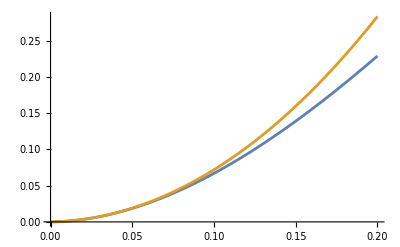

```mathematica
β={1/6,1/7,1/7,1/10};
ΦU1[x_,y_]:=Re@Sum[(y[[i;;i,All]].y[[i;;i,All]]†)[[1,1]],{i,1,4}];
residueNormSquared[x_,y_]:=Re@Sum[1/(2β[[i]])Tr[y[[i;;i,All]]†.x[[All,i;;i]]†.x[[All,i;;i]].y[[i;;i,All]]],{i,1,4}];
testVal={.4,.4,t};
ΦU1@@{xMatrixValued@@testVal,yMatrixValued@@testVal};
residueNormSquared@@{xMatrixValued@@testVal,yMatrixValued@@testVal};
Plot[{%%,%},{t,0,0.2}]
```